```mathematica
Clear[a, b, c, d]
```

```mathematica
(* Logistic 4 Param equation #6 for Mar8,returns dose concentration given instrument response.  Asymptotes are 'a+d' on the left, and 'd' on the right. *)
```

```mathematica
logistic4p[r_]:=  a/(1+(r/b)^c)+d
```

```mathematica
(* Invert the equation to obtain instrument response as a function of dose concentration. *)
```

```mathematica
Solve[t==logistic4p[r], r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→b (-1-a/(d-t))^(1/c)}}

```mathematica
(* Set second derivative to zero to obtain dose concentration value for which instrument response is at its midpoint. *)
```

```mathematica
Simplify[logistic4p''[r]==0]
```

(a c (r/b)^c (1+(r/b)^c+c (-1+(r/b)^c)))/(r (1+(r/b)^c))==0

```mathematica
Solve[1+(r/b)^c+c (-1+(r/b)^c)==0, r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→b ((-1+c)/(1+c))^(1/c)}}

```mathematica
(* Example curve using coefficients obtained in the Excel Solver. *)
```

```mathematica
a=-1.125;b=0.525; c=3.2; d=1.125; f=0
```

0

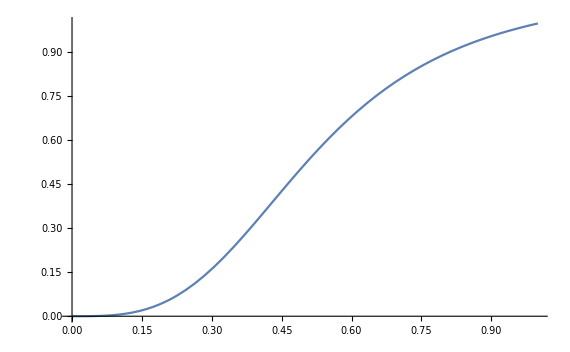

```mathematica
Plot[d+a/(1+(r/b)^c), {r, 0, 1}]
```